```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["Grad_PHANTOM.json","RawJSON"];
```

```mathematica
Keys[data]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
data[["1"]][["5"]][["1"]][["F"]]
data[["2"]][["5"]][["1"]][["F"]]
data[["3"]][["5"]][["1"]][["F"]]
```

{1.1,-1.04083×10^-17,-6.93889×10^-18,0.953672,0.953253}

{1.2,-2.08167×10^-17,-6.93889×10^-18,0.913177,0.912565}

{1.3,-4.16334×10^-17,0.,0.877445,0.876671}

```mathematica
xcoords = Table[0,{i, Length[Keys[data]]}];
ycoords = xcoords;
frames = xcoords;
```

```mathematica
For[i=1, i <= 10, i++,
	frame = i;
	xcoords[[i]] = data[[i]][["6"]][["1"]][["x"]];
	ycoords[[i]] = data[[i]][["6"]][["1"]][["y"]];
	frames[[i]] = i;
	(*Print[data[[i]][["5"]][["1"]][["F"]]];*)
	
]
```

```mathematica
xcoords
```

{0.116229,0.126795,0.137361,0.147927,0.158494,0.16906,0.179626,0.190192,0.200759,0.211325}

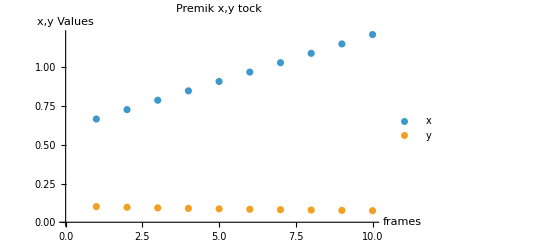

```mathematica
tockex = Transpose[{frames,xcoords}];
tockey =  Transpose[{frames,ycoords}];
ListPlot[{tockex, tockey}, PlotLabel->"Premik x,y tock", PlotLegends->{"x","y"},AxesLabel->{"frames","x,y Values"}]
```